# EIWL Sections 47, 48

## Section 47

```mathematica
Module[{a,i},a=0;For[i=1,i≤1000,i++,a=i*(i+1)+a];a]
```

334334000

```mathematica
Total[Table[i*(i+1),{i,1,1000}]]
```

334334000

```mathematica
Module[{a,i},a=x;For[i=1,i≤10,i++,a=1/(1+a)];a]
```

1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x))))))))))

```mathematica
Nest[1/(1+#)&,x,10]
```

1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+x))))))))))

```mathematica
Module[{i,j,a},a={};For[i=1,i≤10,i++,For[j=1,j≤10,j++,a=Join[a,{i,j}]]];a]
```

{1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,2,10,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,3,10,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,4,10,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,5,10,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,6,10,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,7,10,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,8,10,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,9,10,10,1,10,2,10,3,10,4,10,5,10,6,10,7,10,8,10,9,10,10}

```mathematica
Flatten[Table[Join[{i},{j}],{i,1,10},{j,1,10}]]
```

{1,1,1,2,1,3,1,4,1,5,1,6,1,7,1,8,1,9,1,10,2,1,2,2,2,3,2,4,2,5,2,6,2,7,2,8,2,9,2,10,3,1,3,2,3,3,3,4,3,5,3,6,3,7,3,8,3,9,3,10,4,1,4,2,4,3,4,4,4,5,4,6,4,7,4,8,4,9,4,10,5,1,5,2,5,3,5,4,5,5,5,6,5,7,5,8,5,9,5,10,6,1,6,2,6,3,6,4,6,5,6,6,6,7,6,8,6,9,6,10,7,1,7,2,7,3,7,4,7,5,7,6,7,7,7,8,7,9,7,10,8,1,8,2,8,3,8,4,8,5,8,6,8,7,8,8,8,9,8,10,9,1,9,2,9,3,9,4,9,5,9,6,9,7,9,8,9,9,9,10,10,1,10,2,10,3,10,4,10,5,10,6,10,7,10,8,10,9,10,10}

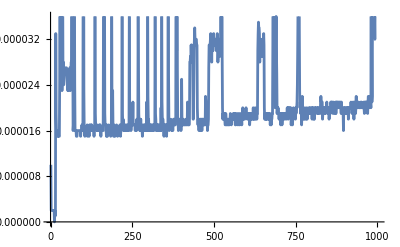

```mathematica
ListLinePlot[Table[First[Timing[n^n]],{n,1,1000}]]
```

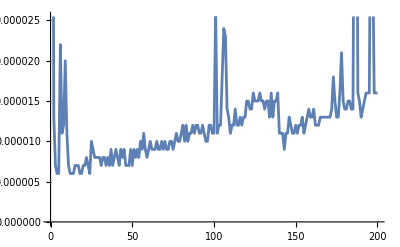

```mathematica
ListLinePlot[Table[First[Timing[Sort[RandomSample[Range[n]]]]],{n,1,200}]]
```

## Section 48

```mathematica
LetterCounts[ToUpperCase[StringJoin[If[StringLength[#]>1,StringTake[#,2],#]&/@WordList[]]]]
```

<|E→7527,A→7525,O→6388,I→5648,R→5309,S→4907,U→4441,C→4365,N→4268,P→3950,L→2958,H→2904,T→2865,D→2741,M→2716,B→2457,F→1840,G→1319,W→1187,V→972,Y→579,X→458,K→330,J→321,Q→306,Z→64|>

```mathematica
Reap[Fold[10Sow[#1]+#2&,{1,2,3,4,5}]]
```

{12345,{{1,12,123,1234}}}

```mathematica
Reap[Nest[If[EvenQ[#],Sow[#/2],3#+1]&,1000,20]]
```

{274,{{500,250,125,188,94,47,71,107,161,242,121,182,91}}}